## Classical energy functions

```mathematica
ClearAll["Global*`"]
```

The expressions of the energy function ℋ(θ,φ) for an axis quantization

```mathematica
ClassicalEnergy[Ivalues_,jvalues_]:=1/120(Ivalues[[1]]-jvalues[[1]])^2+1/40(Ivalues[[2]]-jvalues[[2]])^2+1/60(Ivalues[[3]]-jvalues[[3]])^2;
```

The expression of the chiral energy function ℋ(θ,φ) for an axis quantization

```mathematica
ClassicalEnergyChiral[Ivalues_,jvalues_]:=1/120(Ivalues[[1]]+jvalues[[1]])^2+1/40(Ivalues[[2]]+jvalues[[2]])^2+1/60(Ivalues[[3]]+jvalues[[3]])^2;
```

The components of the odd-particle angular momentum j={j1,j2,j3}

```mathematica
jvalues[axis_,jspin_,theta_,phi_]:=Piecewise[{{{jspin*Cos[theta],jspin*Sin[theta]*Cos[phi],jspin*Sin[theta]*Sin[phi]}, axis==1}, {{jspin*Sin[theta]*Sin[phi],jspin*Cos[theta],jspin*Sin[theta]*Cos[phi]}, axis==2}, {{jspin*Sin[theta]*Cos[phi],jspin*Sin[theta]*Sin[phi],jspin*Cos[theta]}, axis==3}}];
```

The components of the total angular momentum I={I1,I2,I3}

```mathematica
Ivalues[axis_,Ispin_,theta_,phi_]:=Piecewise[{{{Ispin*Cos[theta],Ispin*Sin[theta]*Cos[phi],Ispin*Sin[theta]*Sin[phi]}, axis==1}, {{Ispin*Sin[theta]*Sin[phi],Ispin*Cos[theta],Ispin*Sin[theta]*Cos[phi]}, axis==2}, {{Ispin*Sin[theta]*Cos[phi],Ispin*Sin[theta]*Sin[phi],Ispin*Cos[theta]}, axis==3}}];
```

## Numerical calculations

Fix the total angular momentum and the odd-particle angular momentum

```mathematica
jconst=N[13/2];
Iconst=N[35/2];
thconst=N[π/4];
phiconst=N[π/4];
```

```mathematica
j1values=jvalues[1,jconst,thconst,phiconst];
j2values=jvalues[2,jconst,thconst,phiconst];
j3values=jvalues[3,jconst,thconst,phiconst];
I1values[th_,phi_]:=Ivalues[1,Iconst,th,phi];
I2values[th_,phi_]:=Ivalues[2,Iconst,th,phi];
I3values[th_,phi_]:=Ivalues[3,Iconst,th,phi];
Energy1Axis[th_,phi_]:=ClassicalEnergy[I1values[th,phi],j1values];
Energy2Axis[th_,phi_]:=ClassicalEnergy[I2values[th,phi],j2values];
Energy3Axis[th_,phi_]:=ClassicalEnergy[I3values[th,phi],j3values];
Chiral1Axis[th_,phi_]:=ClassicalEnergyChiral[I1values[th,phi],j1values];
Chiral2Axis[th_,phi_]:=ClassicalEnergyChiral[I2values[th,phi],j2values];
Chiral3Axis[th_,phi_]:=ClassicalEnergyChiral[I3values[th,phi],j3values];
```

```mathematica
(* numerical test for the classical energy function *)
Print[N[Chiral1Axis[1,1]]," ",N[Chiral2Axis[1,1]]," ",N[Chiral3Axis[1,1]]]
Print[N[Energy1Axis[1,1]]," ",N[Energy2Axis[1,1]]," ",N[Energy3Axis[1,1]]]
```

8.86242 9.06789 10.4535

2.14322 1.65579 2.66717

## Helper functions

```mathematica
export[path_,object_]:=Export[StringTemplate["````.pdf"][NotebookDirectory[],path],object,ImageResolution->1200];
contour1[function_]:=ContourPlot[function[th,phi],{phi,-Pi,Pi},{th,0,Pi},AspectRatio->Automatic,ImageSize->{520,320},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"φ [rad]","θ [rad]"},LabelStyle->{19,Bold,Black,FontFamily->"Times"},Contours->11,PlotLegends->BarLegend[Automatic,None]];
contour2[function_]:=ContourPlot[function[th,phi],{phi,-Pi,Pi},{th,0,Pi},AspectRatio->Automatic,ImageSize->{520,320},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"φ [rad]","θ [rad]"},LabelStyle->{19,Bold,Black,FontFamily->"Times"},Contours->11,PlotLegends->BarLegend[Automatic,None],ColorFunction->"BlueGreenYellow"];
```

### Export the plots

```mathematica
cp1Axis=Show[contour1[Energy1Axis]];
cp1AxisChiral=Show[contour2[Chiral1Axis]];
cp2Axis=Show[contour1[Energy2Axis]];
cp2AxisChiral=Show[contour2[Chiral2Axis]];
cp3Axis=Show[contour1[Energy3Axis]];
cp3AxisChiral=Show[contour2[Chiral3Axis]];
export["Contour1Axis",cp1Axis];
export["Contour1AxisChiral",cp1AxisChiral];
export["Contour2Axis",cp2Axis];
export["Contour2AxisChiral",cp2AxisChiral];
export["Contour3Axis",cp3Axis];
export["Contour3AxisChiral",cp3AxisChiral];
cp1Axis
cp2Axis
cp3Axis
cp1AxisChiral
cp2AxisChiral
cp3AxisChiral
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Create 1-dimensional plot of H

The graphical representation of H(φ), where the polar angle θ is fixed

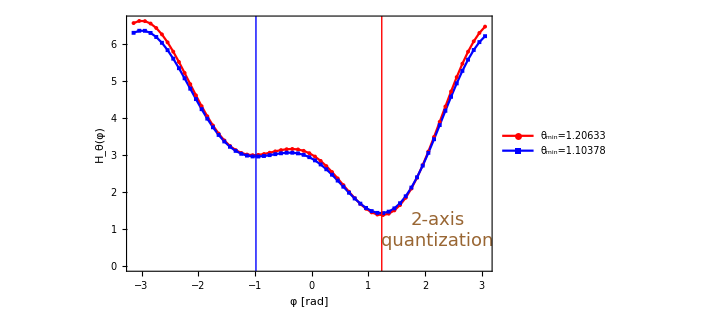

```mathematica
ClEn2Axistheta[th_]:=Table[{phi,Energy2Axis[th,phi]},{phi,-Pi,Pi,0.1}];
plotClEn[plotlist_]:=
ListPlot[Table[plotlist[[i]],{i,1,Length[plotlist]}],Frame->True,Axes->True,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Tiny},FrameStyle->Directive[Black,Thick],FrameLabel->{"φ [rad]","H_θ(φ)"},ImageSize->{520,320},LabelStyle->{21,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{Style["θ_min=1.20633",16],Style["θ_min=1.10378",16]},Scaled[{0.18,0.18}]],Epilog->Inset[Style["2-axis\nquantization",Brown,Italic,18,FontFamily->"Times"],Scaled[{0.85,0.16}]],PlotStyle->{{Red},{Blue}}];
HphiVariation2axis=Show[plotClEn[{ClEn2Axistheta[1.20633],ClEn2Axistheta[1.10378]}],Graphics[{Blue,Line[{{-0.982924,-1},{-0.982924,8}}]}],Graphics[{Red,Line[{{1.23616,-1},{1.23616,8}}]}]];
export["classicalEnergy_phiVariation",HphiVariation2axis];
HphiVariation2axis
```

## Minimization procedure

```mathematica
minpoints1Axis[thlims_,philims_]:=NMinimize[{Energy1Axis[th,phi],thlims[[1]]≤th≤thlims[[2]],philims[[1]]≤phi≤philims[[2]]},{th,phi}];
minpoints2Axis[thlims_,philims_]:=NMinimize[{Energy2Axis[th,phi],thlims[[1]]≤th≤thlims[[2]],philims[[1]]≤phi≤philims[[2]]},{th,phi}];
minpoints3Axis[thlims_,philims_]:=NMinimize[{Energy3Axis[th,phi],thlims[[1]]≤th≤thlims[[2]],philims[[1]]≤phi≤philims[[2]]},{th,phi}];
(*minpoints1AxisChiral[thlims_,philims_]:=NMinimize[{Chiral1Axis[th,phi],thlims[[1]]≤th≤thlims[[2]],philims[[1]]≤phi≤philims[[2]]},{th,phi}];*)
getMinPoints[quantization_]:={Values@quantization[[2]][[1]],Values@quantization[[2]][[2]],quantization[[1]]};
(* For a set of given (θ,φ) find the corresponding list of total angular momentum components Subscript[I, 1] Subscript[I, 2] Subscript[I, 3]*)
minSpins[thmin_,phimin_]:={I1values[thmin,phimin],I2values[thmin,phimin],I3values[thmin,phimin]};
getMinSpins[case_,thmin_,phimin_]:=minSpins[thmin,phimin][[case]];
(* Embed the spin values and the polar coordinates in a List form *)
getPointLabel[case_,quantization_]:={StringTemplate["``-axis"][case],getMinPoints[quantization][[1]],getMinPoints[quantization][[2]],getMinPoints[quantization][[3]],getMinSpins[case,getMinPoints[quantization][[1]],getMinPoints[quantization][[2]]]};
```

The list with minimal points of H, evaluated for each quantization case

```mathematica
p1Axis=getMinPoints[minpoints1Axis[{0,π},{0,π}]];
p2Axis1=getMinPoints[minpoints2Axis[{0,π},{0,π}]];
p2Axis2=getMinPoints[minpoints2Axis[{0,π},{-π,-0.5}]];
p3Axis=getMinPoints[minpoints3Axis[{0,π},{0,π}]];
```

```mathematica
export["AllPoints",Grid[{{"Axis quantization","θ_min","φ_min","H_min(θ,φ)"},getPointLabel[1,minpoints1Axis[{0,π},{0,π}]],getPointLabel[2,minpoints2Axis[{0,π},{0,π}]],getPointLabel[2,minpoints2Axis[{0,π},{-π,-0.5}]],getPointLabel[3,minpoints3Axis[{0,π},{0,π}]]},ItemStyle->{14,Bold,Black,FontFamily->"Helvetica"},Frame->All]];
```